```mathematica
FindAlwaysDifferent[g_]:=Block[{sol =Solve[ ToEquations[g],SymbolRange[g]],result={},localsol,count},
count=Length[sol];
Table[
With[
{v1=e[[1]],v2=e[[2]]},
If[VertexDegree[g,v1]>3&&VertexDegree[g,v2]>3,
localsol=Map[{Symbol["x"<>ToString[v1]],Symbol["x"<>ToString[v2]]}/.#&,sol];
localsol=Select[localsol,#[[1]]≠#[[2]]&];
localsol=Length[localsol];
If[localsol==count,
AppendTo[result,v1<->v2]
]
]
]
,{e,EdgeList[GraphComplement[g]]}
];
result
]
```

```mathematica
FindAlwaysDifferent[ReadGrof[3]]
```

{1<->4}

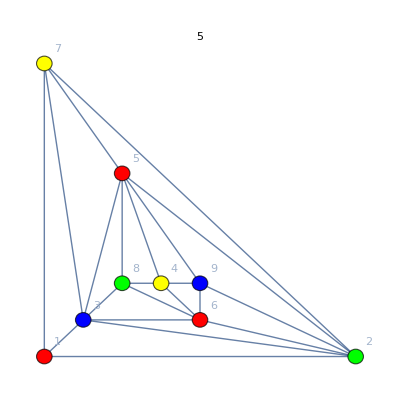
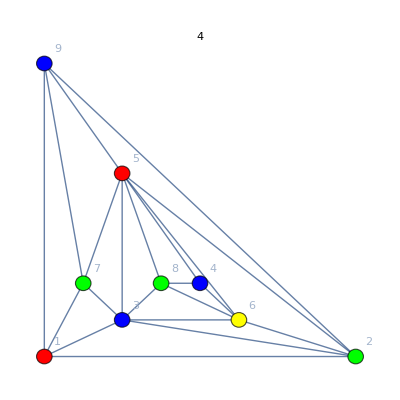
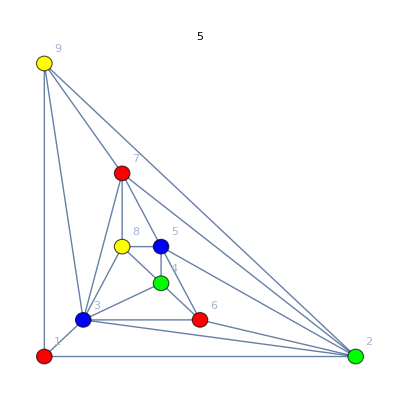
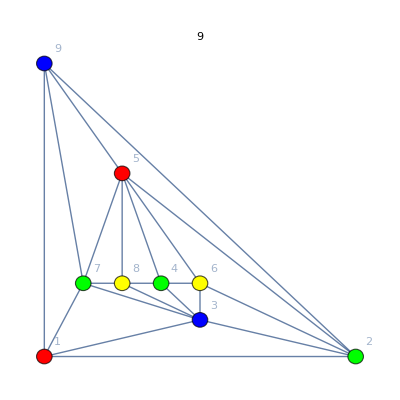
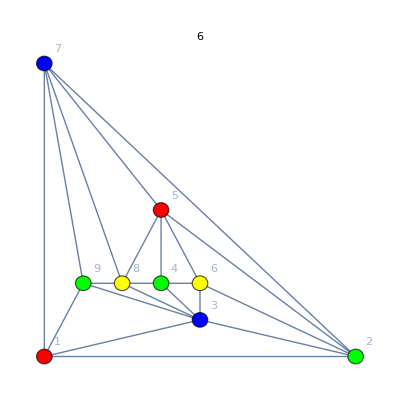
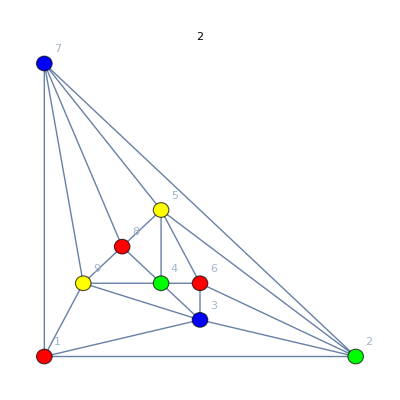
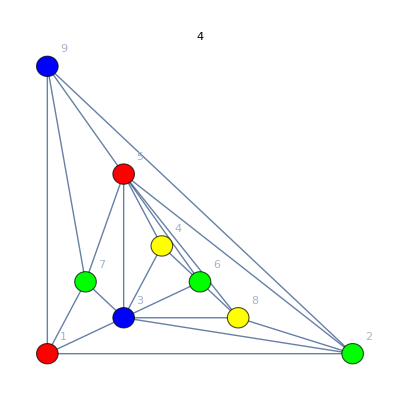
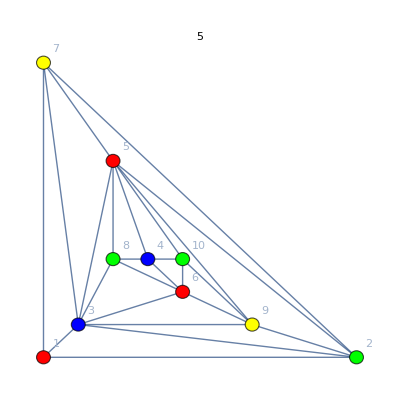
26 | -Graphics- | 7<->6
30 | -Graphics- | 1<->8
9<->8
39 | -Graphics- | 9<->5
40 | -Graphics- | 2<->8
7<->6
41 | -Graphics- | 1<->4
2<->8
9<->6
46 | -Graphics- | 1<->5
1<->4
2<->8
3<->8
7<->6
9<->6
56 | -Graphics- | 1<->6
9<->6
76 | -Graphics- | 2<->6
7<->6
7<->10
78 | -Graphics- | 1<->6
2<->8
10<->6
79 | -Graphics- | 2<->8
10<->8
88 | -Graphics- | 7<->6
89 | -Graphics- | 10<->8
90 | -Graphics- | 7<->5
91 | -Graphics- | 2<->8
10<->9
93 | -Graphics- | 7<->6
7<->10
97 | -Graphics- | 10<->6
10<->8
99 | -Graphics- | 7<->10
100 | -Graphics- | 7<->6
102 | -Graphics- | 1<->6
1<->8
107 | -Graphics- | 1<->8
2<->5
7<->9
108 | -Graphics- | 2<->4
3<->4
7<->6
7<->8
9<->10
9<->5
110 | -Graphics- | 10<->9
10<->8
10<->4
6<->7
111 | -Graphics- | 7<->6
10<->6
113 | -Graphics- | 7<->4
114 | -Graphics- | 7<->6
115 | -Graphics- | 1<->9
1<->8
1<->4
7<->6
116 | -Graphics- | 7<->6
117 | -Graphics- | 7<->6
118 | -Graphics- | 7<->6
119 | -Graphics- | 7<->6
120 | -Graphics- | 1<->4
10<->6
121 | -Graphics- | 3<->9
10<->8
122 | -Graphics- | 2<->8
3<->9
7<->6
7<->4
9<->5
10<->8
123 | -Graphics- | 7<->4
125 | -Graphics- | 1<->8
1<->9
2<->9
7<->9
10<->8
136 | -Graphics- | 1<->8
1<->9
2<->9
7<->9
10<->8
146 | -Graphics- | 2<->4
7<->9
6<->10
147 | -Graphics- | 9<->8
10<->8
149 | -Graphics- | 9<->5
151 | -Graphics- | 9<->6
9<->10
9<->4
7<->8
7<->4
158 | -Graphics- | 9<->10
9<->8
160 | -Graphics- | 1<->6
1<->8
9<->8
161 | -Graphics- | 1<->4
9<->8
162 | -Graphics- | 1<->8
9<->8
163 | -Graphics- | 1<->8
9<->8
164 | -Graphics- | 1<->8
9<->8
165 | -Graphics- | 1<->8
9<->8
166 | -Graphics- | 1<->8
9<->8
167 | -Graphics- | 1<->8
9<->8
168 | -Graphics- | 1<->8
9<->8
170 | -Graphics- | 2<->10
7<->6
9<->8
202 | -Graphics- | 1<->4
206 | -Graphics- | 7<->6
9<->8
208 | -Graphics- | 2<->4
7<->6
214 | -Graphics- | 2<->4
7<->6
9<->8
215 | -Graphics- | 2<->4
7<->6
10<->9
216 | -Graphics- | 2<->8
3<->10
7<->9
6<->8
9<->5
10<->4
217 | -Graphics- | 10<->4
218 | -Graphics- | 1<->4
7<->6
7<->9
10<->4
219 | -Graphics- | 3<->5
6<->10
9<->8
224 | -Graphics- | 1<->4
2<->8
2<->5
7<->6
7<->9
10<->4
225 | -Graphics- | 10<->5
10<->8
5<->9
226 | -Graphics- | 9<->5
227 | -Graphics- | 9<->5
228 | -Graphics- | 9<->5
229 | -Graphics- | 9<->5
230 | -Graphics- | 9<->5
231 | -Graphics- | 9<->5
232 | -Graphics- | 9<->5
250 | -Graphics- | 7<->10
9<->10
271 | -Graphics- | 1<->6
2<->9
10<->6
278 | -Graphics- | 9<->6
10<->6
282 | -Graphics- | 1<->6
9<->6
283 | -Graphics- | 1<->6
9<->6
308 | -Graphics- | 1<->6
1<->10
2<->8
2<->10
7<->10
11<->6
9<->10
309 | -Graphics- | 2<->8
2<->10
7<->10
9<->10
11<->8
312 | -Graphics- | 2<->8
2<->10
7<->6
313 | -Graphics- | 7<->11
7<->6
314 | -Graphics- | 2<->11
2<->4
2<->10
7<->6
7<->8
9<->8
318 | -Graphics- | 2<->10
7<->10
11<->10
319 | -Graphics- | 2<->6
7<->6
7<->11
321 | -Graphics- | 2<->8
2<->4
2<->11
7<->6
7<->4
7<->10
9<->4
9<->10
334 | -Graphics- | 1<->10
2<->8
2<->10
7<->10
11<->6
11<->8
9<->10
335 | -Graphics- | 2<->10
7<->10
9<->10
11<->8
336 | -Graphics- | 3<->10
7<->5
337 | -Graphics- | 2<->8
11<->9
339 | -Graphics- | 3<->8
3<->10
7<->10
340 | -Graphics- | 7<->6
9<->11
343 | -Graphics- | 7<->11
11<->10
345 | -Graphics- | 2<->11
2<->10
7<->6
346 | -Graphics- | 2<->4
7<->11
7<->6
347 | -Graphics- | 7<->6
348 | -Graphics- | 7<->6
7<->11
350 | -Graphics- | 1<->6
1<->10
2<->8
2<->10
7<->10
11<->6
9<->10
351 | -Graphics- | 2<->8
2<->10
7<->10
9<->10
11<->8
354 | -Graphics- | 2<->8
2<->10
7<->6
7<->8
9<->8
356 | -Graphics- | 7<->11
7<->6
357 | -Graphics- | 2<->11
2<->10
7<->6
359 | -Graphics- | 2<->10
7<->10
11<->10
360 | -Graphics- | 2<->6
7<->6
7<->11
372 | -Graphics- | 1<->10
2<->8
2<->10
7<->10
11<->6
11<->8
9<->10
373 | -Graphics- | 2<->10
7<->10
9<->10
11<->8
374 | -Graphics- | 3<->10
7<->5
375 | -Graphics- | 2<->8
11<->9
377 | -Graphics- | 3<->8
3<->10
7<->10
380 | -Graphics- | 7<->11
11<->10
381 | -Graphics- | 7<->6
382 | -Graphics- | 2<->6
11<->9
11<->8
11<->4
11<->10
7<->6
7<->10
383 | -Graphics- | 1<->10
2<->6
7<->6
11<->6
384 | -Graphics- | 7<->6
11<->6
385 | -Graphics- | 7<->6
7<->10
386 | -Graphics- | 2<->4
7<->6
7<->10
387 | -Graphics- | 2<->6
7<->11
7<->6
7<->10
388 | -Graphics- | 3<->10
7<->9
9<->8
389 | -Graphics- | 2<->6
7<->11
7<->10
390 | -Graphics- | 2<->4
3<->10
11<->8
391 | -Graphics- | 2<->4
7<->6
7<->10
7<->11
392 | -Graphics- | 2<->6
7<->6
7<->10
393 | -Graphics- | 2<->6
7<->6
7<->10
394 | -Graphics- | 2<->6
7<->6
7<->10
395 | -Graphics- | 2<->6
7<->6
7<->10
396 | -Graphics- | 2<->6
7<->6
7<->10
397 | -Graphics- | 2<->6
7<->6
7<->10
398 | -Graphics- | 2<->6
7<->6
7<->10
399 | -Graphics- | 2<->6
7<->6
7<->10
400 | -Graphics- | 2<->6
7<->6
7<->10
401 | -Graphics- | 2<->6
7<->6
7<->10
402 | -Graphics- | 7<->6
11<->6
11<->8
403 | -Graphics- | 2<->4
11<->6
404 | -Graphics- | 2<->4
9<->8
11<->10
405 | -Graphics- | 7<->6
406 | -Graphics- | 2<->8
2<->4
2<->10
7<->5
7<->6
7<->10
11<->6
408 | -Graphics- | 2<->4
7<->6
9<->11
409 | -Graphics- | 2<->6
2<->8
3<->6
7<->11
7<->6
7<->10
410 | -Graphics- | 2<->4
7<->6
7<->10
411 | -Graphics- | 2<->4
7<->6
7<->10
7<->11
412 | -Graphics- | 2<->4
3<->10
9<->8
413 | -Graphics- | 2<->6
2<->4
3<->10
7<->8
7<->10
5<->10
9<->8
11<->8
414 | -Graphics- | 2<->8
11<->8
415 | -Graphics- | 2<->8
10<->6
11<->6
418 | -Graphics- | 2<->8
2<->4
10<->9
10<->6
10<->11
10<->4
7<->6
419 | -Graphics- | 10<->9
10<->8
10<->6
7<->11
7<->6
421 | -Graphics- | 10<->9
10<->6
10<->8
431 | -Graphics- | 10<->11
10<->8
10<->4
7<->6
432 | -Graphics- | 10<->11
11<->8
433 | -Graphics- | 10<->5
10<->8
5<->7
435 | -Graphics- | 3<->8
10<->5
436 | -Graphics- | 7<->6
9<->11
437 | -Graphics- | 2<->8
9<->11
439 | -Graphics- | 10<->9
10<->8
10<->11
7<->6
7<->11
440 | -Graphics- | 10<->9
10<->8
10<->6
7<->11
441 | -Graphics- | 1<->9
1<->6
1<->8
2<->8
10<->6
443 | -Graphics- | 1<->6
2<->8
2<->4
10<->6
444 | -Graphics- | 1<->6
10<->11
445 | -Graphics- | 1<->8
1<->9
2<->6
10<->8
10<->9
11<->8
447 | -Graphics- | 1<->6
2<->8
10<->6
448 | -Graphics- | 1<->6
2<->8
10<->6
449 | -Graphics- | 1<->6
2<->8
10<->6
450 | -Graphics- | 1<->6
2<->8
10<->6
451 | -Graphics- | 1<->6
2<->8
10<->6
452 | -Graphics- | 1<->6
2<->8
10<->6
453 | -Graphics- | 1<->6
2<->8
10<->6
454 | -Graphics- | 1<->6
2<->8
10<->6
455 | -Graphics- | 1<->6
2<->8
10<->6
456 | -Graphics- | 10<->6
459 | -Graphics- | 1<->11
1<->6
2<->6
2<->8
3<->8
7<->6
10<->11
460 | -Graphics- | 1<->11
10<->6
461 | -Graphics- | 7<->11
10<->11
463 | -Graphics- | 2<->8
464 | -Graphics- | 2<->8
7<->6
11<->8
8<->10
465 | -Graphics- | 2<->6
2<->8
10<->8
466 | -Graphics- | 2<->8
10<->8
467 | -Graphics- | 2<->8
10<->8
468 | -Graphics- | 2<->8
10<->8
469 | -Graphics- | 2<->8
10<->8
470 | -Graphics- | 2<->8
10<->8
471 | -Graphics- | 2<->8
10<->8
472 | -Graphics- | 2<->8
10<->8
473 | -Graphics- | 2<->8
10<->8
474 | -Graphics- | 2<->8
10<->8
475 | -Graphics- | 2<->8
10<->8
476 | -Graphics- | 2<->11
7<->8
9<->8
10<->8
10<->11
477 | -Graphics- | 2<->8
479 | -Graphics- | 2<->8
7<->6
9<->11
480 | -Graphics- | 2<->6
2<->8
3<->8
7<->6
10<->8
482 | -Graphics- | 3<->9
7<->6
10<->8
483 | -Graphics- | 10<->8
485 | -Graphics- | 2<->8
7<->6
489 | -Graphics- | 2<->8
7<->6
11<->10
490 | -Graphics- | 2<->8
7<->6
9<->10
491 | -Graphics- | 7<->11
7<->9

```mathematica
Select[
Monitor[
Table[
With[
{g=ReadGrof[k]},
If[ChromaticPolynomial[g,4]≠24 ,
{k,PaintGraph2First[g,"True",VertexLabels->"Name",GraphLayout->"PlanarEmbedding",VertexSize->Large,PlotLabel->ChromaticPolynomial[g,4]/24],FindAlwaysDifferent[g]},
{k,Null,{}}
]
],
{k,1,500}
],
k],
#[[3]]≠{}&
]//TableForm
```

```mathematica
Graph[-Graphics-,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-

```mathematica
Select[
With[
{g=ReadGrof[40]},
Map[{x6,x7}/.#&,Solve[ ToEquations[g],SymbolRange[g]]]
],
#[[1]]==#[[2]]&
]
```

{}

```mathematica
EdgeList[GraphComplement[ReadGrof[40]]]//Sort
```

{1<->4,1<->5,1<->6,1<->8,2<->4,2<->7,2<->8,3<->5,3<->9,6<->8,7<->4,7<->6,9<->4,9<->6,9<->8}

```mathematica
Select[
Monitor[
Table[
With[
{g=Graph[plantri[[k]]]},
{k,VertexCount[g],g,FindAlwaysDifferent[g]}
],
{k,1,10}
],
k],
#[[3]]≠{}&
]//TableForm
```

{}

```mathematica
Table[
With[
{g=Graph[plantri[[k]]]},
{k,VertexCount[g],ChromaticPolynomial[g,4]/24}
],
{k,1,15}
]
```

{{1,12,10},{2,14,20},{3,15,32},{4,16,30},{5,16,27},{6,16,42},{7,17,16},{8,17,22},{9,17,32},{10,17,40},{11,18,44},{12,18,30},{13,18,48},{14,18,38},{15,18,52}}